## 计算物理作业2

Baker’s map

Baker’s map是对单位方格里面的点进行的映射，其迭代方程如下：
-Graphics-
不难看出，其操作首先将单位方格压缩，之后再剪开粘合，因而该操作类似于揉面团的过程。我们定义迭代函数f如下：

```mathematica
f[x_,y_]:=If[(x<0.5)&&(x>0),Return[{2x,y/2}],Return[{2-2x,1-y/2}]]
```

先对单个点进行迭代，绘制其运动的图像：

{{0.249743,0.162082}}

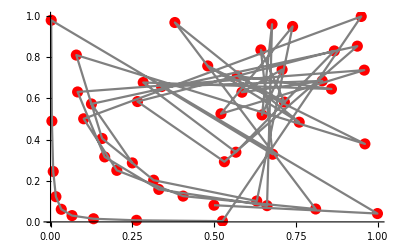

```mathematica
init=Table[{RandomReal[],RandomReal[]},1]
data=init;
p=Partition[Table[{
data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];
data
},50]//Flatten,2];
ListPlot[p,PlotStyle->{Red,PointSize[0.02]}]~Show~ListLinePlot[p,PlotRange->{{0,1},{0,1}},PlotStyle->Gray]
```

可见其运动轨迹在单位方格内跳跃，若将上下两层染色，再进行迭代，效果如下：

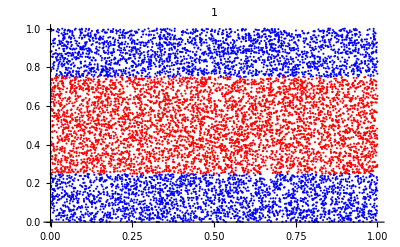
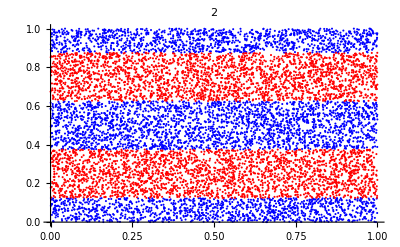
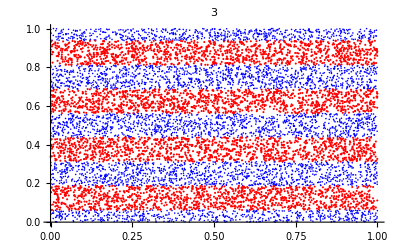
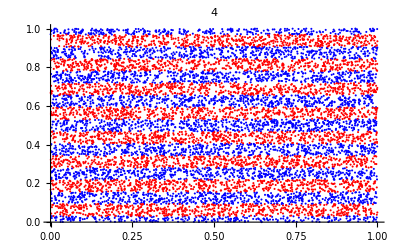
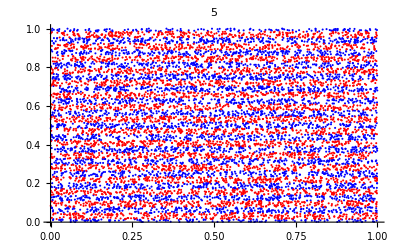

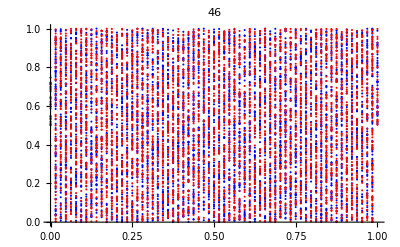
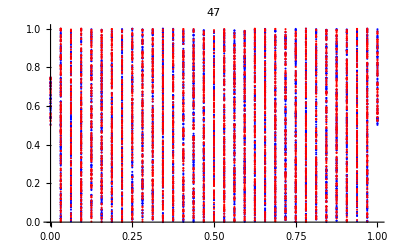
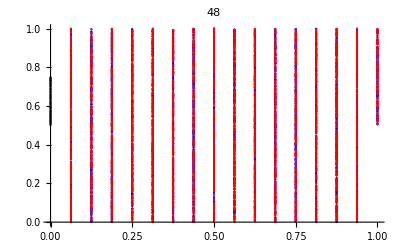

```mathematica
init=Table[{RandomReal[],0.5*RandomReal[]},5000];
init2=Table[{RandomReal[],0.5+0.5*RandomReal[]},5000];
data=init;
data2=init2;
Table[{
data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];
data2=Table[f[data2[[i]][[1]],data2[[i]][[2]]],{i,1,Length[init]}];
ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},{0,1}},PlotLabel->iii]~Show~ListPlot[data2,PlotStyle->Red,PlotRange->{{0,1},{0,1}}]
},{iii,1,5,1}]
Table[{
data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];
data2=Table[f[data2[[i]][[1]],data2[[i]][[2]]],{i,1,Length[init]}];
},{iii,6,45,1}];
Table[{
data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];
data2=Table[f[data2[[i]][[1]],data2[[i]][[2]]],{i,1,Length[init]}];
ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},{0,1}},PlotLabel->iii]~Show~ListPlot[data2,PlotStyle->Red,PlotRange->{{0,1},{0,1}}]
},{iii,46,50,1}]
```

可见，刚开始时，两种颜色的点像揉面团一样相互混合。之后，当迭代次数达到46左右，开始出现纵向的分层，之后所有的点都逐渐聚集，从而出现上述图景。